```mathematica
f[V_]:=(2(0.7292+V))/(1.602176565*10^-19*11.7*8.854187817*10^-12*2*10^-15)
Plot[{Piecewise[{{f[Subscript[V, R]],Subscript[V, R]<0.5}},None],Piecewise[{{f[Subscript[V, R]],Subscript[V, R]≥0.5}},None]},{Subscript[V, R],-0.7292,5},PlotStyle->{Dashed,Blue}]
```

-Graphics-

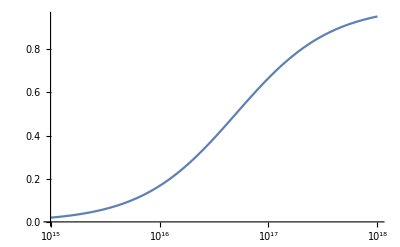

```mathematica
LogLinearPlot[1/(1+(5*10^16)/Subscript[N, a]),{Subscript[N, a],10^15,10^18}]
```

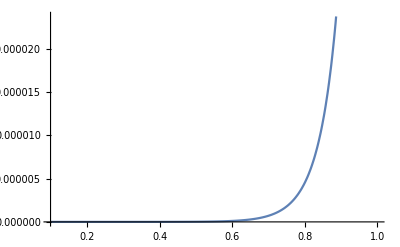

```mathematica
Plot[3.088*10^-21*(Exp[38.68 Subscript[V, D]]-1)+1.226*10^-12*Exp[19.34 Subscript[V, D]]*√(1.279-Subscript[V, D]),{Subscript[V, D],0.1,1}]
```

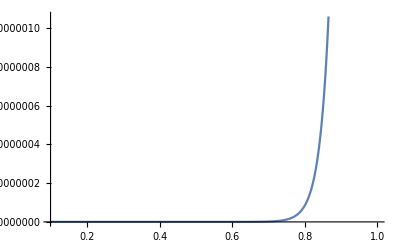

```mathematica
Plot[3.088*10^-21*(Exp[38.68 Subscript[V, D]]-1),{Subscript[V, D],0.1,1}]
```